## Load package

```mathematica
(*Quit*)
```

```mathematica
pathToPackage=FileNameJoin[{NotebookDirectory[],"package.wl"}];
Get[pathToPackage];
```

```mathematica
(*Quit*)
```

## defining lengthList

```mathematica
lengthList={};
x=1.0;
While[x>0.01,
AppendTo[lengthList,x];
x=x/2;
];
lengthList
```

{1.,0.5,0.25,0.125,0.0625,0.03125,0.015625}

## main loop

1.

{{{0,0},{1,0},{0,1},{1,1}}}

0.5

{{{0,0},{1,0},{0,1},{1,1}},{{0,1},{0.5,1},{0,1.5},{0.5,1.5}}}

0.25

{{{0,0},{1,0},{0,1},{1,1}},{{0,1},{0.5,1},{0,1.5},{0.5,1.5}},{{0,1.5},{0.25,1.5},{0,1.75},{0.25,1.75}},{{0.5,1},{0.75,1},{0.5,1.25},{0.75,1.25}}}

0.125

{{{0,0},{1,0},{0,1},{1,1}},{{0,1},{0.5,1},{0,1.5},{0.5,1.5}},{{0,1.5},{0.25,1.5},{0,1.75},{0.25,1.75}},{{0.5,1},{0.75,1},{0.5,1.25},{0.75,1.25}},{{0,1.75},{0.125,1.75},{0,1.875},{0.125,1.875}},{{0.25,1.5},{0.375,1.5},{0.25,1.625},{0.375,1.625}},{{0.5,1.25},{0.625,1.25},{0.5,1.375},{0.625,1.375}},{{0.75,1},{0.875,1},{0.75,1.125},{0.875,1.125}}}

0.0625

{{{0,0},{1,0},{0,1},{1,1}},{{0,1},{0.5,1},{0,1.5},{0.5,1.5}},{{0,1.5},{0.25,1.5},{0,1.75},{0.25,1.75}},{{0.5,1},{0.75,1},{0.5,1.25},{0.75,1.25}},{{0,1.75},{0.125,1.75},{0,1.875},{0.125,1.875}},{{0.25,1.5},{0.375,1.5},{0.25,1.625},{0.375,1.625}},{{0.5,1.25},{0.625,1.25},{0.5,1.375},{0.625,1.375}},{{0.75,1},{0.875,1},{0.75,1.125},{0.875,1.125}},{{0,1.875},{0.0625,1.875},{0,1.9375},{0.0625,1.9375}},{{0.125,1.75},{0.1875,1.75},{0.125,1.8125},{0.1875,1.8125}},{{0.25,1.625},{0.3125,1.625},{0.25,1.6875},{0.3125,1.6875}},{{0.375,1.5},{0.4375,1.5},{0.375,1.5625},{0.4375,1.5625}},{{0.5,1.375},{0.5625,1.375},{0.5,1.4375},{0.5625,1.4375}},{{0.625,1.25},{0.6875,1.25},{0.625,1.3125},{0.6875,1.3125}},{{0.75,1.125},{0.8125,1.125},{0.75,1.1875},{0.8125,1.1875}},{{0.875,1},{0.9375,1},{0.875,1.0625},{0.9375,1.0625}}}

0.03125

{{{0,0},{1,0},{0,1},{1,1}},{{0,1},{0.5,1},{0,1.5},{0.5,1.5}},{{0,1.5},{0.25,1.5},{0,1.75},{0.25,1.75}},{{0.5,1},{0.75,1},{0.5,1.25},{0.75,1.25}},{{0,1.75},{0.125,1.75},{0,1.875},{0.125,1.875}},{{0.25,1.5},{0.375,1.5},{0.25,1.625},{0.375,1.625}},{{0.5,1.25},{0.625,1.25},{0.5,1.375},{0.625,1.375}},{{0.75,1},{0.875,1},{0.75,1.125},{0.875,1.125}},{{0,1.875},{0.0625,1.875},{0,1.9375},{0.0625,1.9375}},{{0.125,1.75},{0.1875,1.75},{0.125,1.8125},{0.1875,1.8125}},{{0.25,1.625},{0.3125,1.625},{0.25,1.6875},{0.3125,1.6875}},{{0.375,1.5},{0.4375,1.5},{0.375,1.5625},{0.4375,1.5625}},{{0.5,1.375},{0.5625,1.375},{0.5,1.4375},{0.5625,1.4375}},{{0.625,1.25},{0.6875,1.25},{0.625,1.3125},{0.6875,1.3125}},{{0.75,1.125},{0.8125,1.125},{0.75,1.1875},{0.8125,1.1875}},{{0.875,1},{0.9375,1},{0.875,1.0625},{0.9375,1.0625}},{{0,1.9375},{0.03125,1.9375},{0,1.96875},{0.03125,1.96875}},{{0.0625,1.875},{0.09375,1.875},{0.0625,1.90625},{0.09375,1.90625}},{{0.125,1.8125},{0.15625,1.8125},{0.125,1.84375},{0.15625,1.84375}},{{0.1875,1.75},{0.21875,1.75},{0.1875,1.78125},{0.21875,1.78125}},{{0.25,1.6875},{0.28125,1.6875},{0.25,1.71875},{0.28125,1.71875}},{{0.3125,1.625},{0.34375,1.625},{0.3125,1.65625},{0.34375,1.65625}},{{0.375,1.5625},{0.40625,1.5625},{0.375,1.59375},{0.40625,1.59375}},{{0.4375,1.5},{0.46875,1.5},{0.4375,1.53125},{0.46875,1.53125}},{{0.5,1.4375},{0.53125,1.4375},{0.5,1.46875},{0.53125,1.46875}},{{0.5625,1.375},{0.59375,1.375},{0.5625,1.40625},{0.59375,1.40625}},{{0.625,1.3125},{0.65625,1.3125},{0.625,1.34375},{0.65625,1.34375}},{{0.6875,1.25},{0.71875,1.25},{0.6875,1.28125},{0.71875,1.28125}},{{0.75,1.1875},{0.78125,1.1875},{0.75,1.21875},{0.78125,1.21875}},{{0.8125,1.125},{0.84375,1.125},{0.8125,1.15625},{0.84375,1.15625}},{{0.875,1.0625},{0.90625,1.0625},{0.875,1.09375},{0.90625,1.09375}},{{0.9375,1},{0.96875,1},{0.9375,1.03125},{0.96875,1.03125}}}

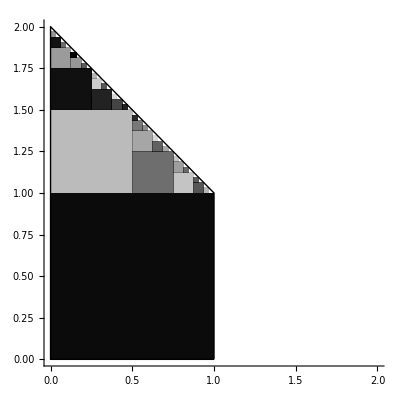

```mathematica
listOutput={};
listCandidates=Table[{{i,j},{i+1,j},{i,j+1},{i+1,j+1}},{i,-5,5,1},{j,-5,5,1}]//Flatten[#,1]&;
Table[

(*finding square inside polygon *)
selectedSquares=Cases[listCandidates,square_/;testSquare[square,D1]];
listOutput=Join[listOutput,selectedSquares];


(*removing square inside polygon *)
listCandidates=Complement[listCandidates,selectedSquares];
(*rplitting remaining squares *)
listCandidates=splitAllSquares[listCandidates,len];
Print[len];
Print[listOutput];


,{len, lengthList[[1;;6]]}];
plotRange={{0,2},{0,2}};
g1=Graphics[Line[D1],PlotRange->plotRange];
D1={{1,0},{1,1},{0,2},{0,0},{1,0}};
Show[
g1,
displaySquare[originalSquare],
displaySquare/@listOutput,

PlotRange->plotRange,
Axes->True
]
```